```mathematica
b1=20;e1=1.1;ap=1;
SetDirectory[NotebookDirectory[]]

(*b1=20;e1=1.1;ap=0.4;*)
pts=5000;max=10 Pi;eta=1/4;


scaleres=10^-16;
scaleorb=10^14;
scaleh=10^-15;
Fp=-0.15842037219323143;
Fx=0.8536550214180404;

cons={c->3 10^8,inc->Pi/4,η ->1/4,y->1/c^2,MS->1.989 10^30,G->6.67430 10^-11,M->2 10^9 MS,R->1.2 10^14(G M)/c^2};

lHub[et_,η_,b_]=Import["lHub.wdx"];
(*U[lH,et]*)
U=u/.FindRoot[#2 Sinh[u]-u==#1//.cons,{u,0}]&;
getu[lH_,et_,η_,b_,PN_]:=(Do[w[0]=U[lH,et];q1=w[d-1];x1=Normal[Series[lHub[et,η,b(G M)/c^2],{y,0,d}]];x2=Expand[PowerExpand[Sum[y^i Coefficient[x1,y^i],{i,1,d}]/.u->q1]];x3=U[lH-x2,et];w[d]=x3;If[d==PN,Return[w[d]]],{d,0,3}])
(*getu[lH_,et_,η_,b_,PN_]*)
(*getu[lH_,et_,η_,b_,PN_]*)
```

/home/subhajit/Dropbox/HyperE2/compare/next

```mathematica
rvbH[et_,u_,b_]=Import["r_vec3PN.wdx"];
```

```mathematica
r[d_,et_,u_,b_]:=Sum[Coefficient[rvbH[et,u,b],y,i] y^i,{i,0,d}]
```

```mathematica
X[d_,et_,u_,b_]:=r[d,et,u,b][[1]];
```

```mathematica
Y[d_,et_,u_,b_]:=r[d,et,u,b][[2]];
```

```mathematica
plotorbit[et_,b_,max_]:=ParametricPlot[{{X[3,et,getu[l,et,eta,b,3],b (G M)/c^2] 1/scaleorb//.cons,Y[3,et,getu[l,et,eta,b,3],b (G M)/c^2] 1/scaleorb//.cons},

{X[1,et,getu[l,et,eta,b,1],b (G M)/c^2] 1/scaleorb//.cons,Y[1,et,getu[l,et,eta,b,1],b (G M)/c^2] 1/scaleorb//.cons},{X[0,et,getu[l,et,eta,b,0],b (G M)/c^2] 1/scaleorb//.cons,Y[0,et,getu[l,et,eta,b,0],b (G M)/c^2] 1/scaleorb//.cons}},{l,-max,max},PlotRange->{{-2,0.2},{-1,1}},PlotLegends->{"3PN","1PN","Newtonian"},PlotLabel->Style["Orbit" (HoldForm["e_t"=et ", b"=b "(G M)/c^2"])": Scaled",FontSize->18]]
```

```mathematica
(*PlotRange->{{-2,0.2},{-1,1}}*)
```

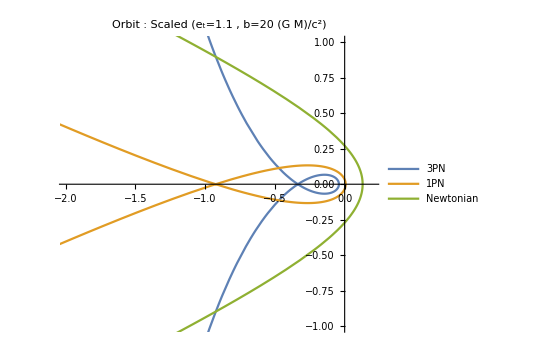

```mathematica
porb=plotorbit[e1,b1,ap]
```

```mathematica
Export[StringJoin["orb",ToString/@Riffle[{e1,b1},"_"],".png"],porb,ImageResolution->200];
```

```mathematica
Hx[et_,u_,b_]=Import["hxb.wdx"];
```

```mathematica
Hp[et_,u_,b_]=Import["hpb.wdx"];
```

```mathematica
hx[d_,et_,u_,b_]:=Sum[Coefficient[Hx[et,u,b],y,i] y^i,{i,0,d}]
```

```mathematica
hp[d_,et_,u_,b_]:=Sum[Coefficient[Hp[et,u,b],y,i] y^i,{i,0,d}]
```

```mathematica
plothx[et_,b_,max_]:=Plot[{hx[3,et,getu[l,et,eta,b,3],b (G M)/c^2] 1/scaleh//.cons,hx[1,et,getu[l,et,eta,b,1],b (G M)/c^2] 1/scaleh//.cons,
hx[0,et,getu[l,et,eta,b,0],b (G M)/c^2] 1/scaleh//.cons},{l,-max,max},PlotRange->All,PlotLegends->{"3PN","1PN","Newtonian"},PlotLabel->Style["H_(X | Q)(l)" (HoldForm["e_t"=et ", b"=b"(G M)/c^2"])": Scaled",FontSize->18]]
```

```mathematica
(*,ImageSize->Scaled[.6]*)
```

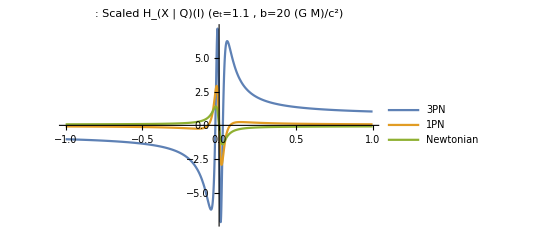

```mathematica
phx=plothx[e1,b1,ap]
```

```mathematica
Export[StringJoin["hx",ToString/@Riffle[{e1,b1},"_"],".png"],phx,ImageResolution->200];
```

```mathematica
plothp[et_,b_,max_]:=Plot[{hp[3,et,getu[l,et,eta,b,3],b (G M)/c^2] 1/scaleh//.cons,hp[1,et,getu[l,et,eta,b,1],b (G M)/c^2] 1/scaleh//.cons,
hp[0,et,getu[l,et,eta,b,0],b (G M)/c^2] 1/scaleh//.cons},{l,-max,max},PlotRange->All,PlotLegends->{"3PN","1PN","Newtonian"},PlotLabel->Style["H_(+|Q)(l)" (HoldForm["e_t"=et ", b"=b"(G M)/c^2"])"Scaled",FontSize->18]]
```

```mathematica
(*ImageSize->Scaled[.6],*)
```

```mathematica
php=plothp[e1,b1,ap]
```

$Aborted

```mathematica
Export[StringJoin["hp",ToString/@Riffle[{e1,b1},"_"],".png"],php,ImageResolution->200];
```

```mathematica
(*--------------------------------------------------------*)
```

```mathematica
tablehx3[et_,b_,max_,pts_]:=Table[hx[3,et,getu[l,et,eta,b,3],b (G M)/c^2]//.cons,{l,-max,max,(2 max)/(pts-1)}]
```

```mathematica
tablehx1[et_,b_,max_,pts_]:=Table[hx[1,et,getu[l,et,eta,b,1],b (G M)/c^2]//.cons,{l,-max,max,(2 max)/(pts-1)}]
```

```mathematica
tablehxQ[et_,b_,max_,pts_]:=Table[hx[0,et,getu[l,et,eta,b,0],b (G M)/c^2]//.cons,{l,-max,max,(2 max)/(pts-1)}]
```

```mathematica
tablehp3[et_,b_,max_,pts_]:=Table[hp[3,et,getu[l,et,eta,b,3],b (G M)/c^2]//.cons,{l,-max,max,(2 max)/(pts-1)}]
```

```mathematica
tablehp1[et_,b_,max_,pts_]:=Table[hp[1,et,getu[l,et,eta,b,1],b (G M)/c^2]//.cons,{l,-max,max,(2 max)/(pts-1)}]
```

```mathematica
tablehpQ[et_,b_,max_,pts_]:=Table[hp[0,et,getu[l,et,eta,b,0],b (G M)/c^2]//.cons,{l,-max,max,(2 max)/(pts-1)}]
```

```mathematica
larr[max_,pts_]:=Table[l/(2 Pi)//N,{l,-max,max,(2 max)/(pts-1)}]
llist=larr[max,pts];
Δ=(Max[llist]-Min[llist])/Length[llist]
```

0.1

```mathematica
sx3=Accumulate[tablehx3[e1,b1,max,pts]] Δ ;
```

```mathematica
sp3=Accumulate[tablehp3[e1,b1,max,pts]]Δ ;
```

```mathematica
sx1=Accumulate[tablehx1[e1,b1,max,pts]] Δ ;
```

```mathematica
sp1=Accumulate[tablehp1[e1,b1,max,pts]]Δ ;
```

```mathematica
sxQ=Accumulate[tablehxQ[e1,b1,max,pts]]Δ;
```

```mathematica
spQ=Accumulate[tablehpQ[e1,b1,max,pts]]Δ;
```

```mathematica
Res3={};For[i=1,i<=Length[llist],i++,AppendTo[Res3,{llist[[i]],(Fp sp3[[i]]+Fx sx3[[i]])/scaleres}]];
```

```mathematica
Res1={};For[i=1,i<=Length[llist],i++,AppendTo[Res1,{llist[[i]],(Fp sp1[[i]]+Fx sx1[[i]])/scaleres}]];
```

```mathematica
ResQ={};For[i=1,i<=Length[llist],i++,AppendTo[ResQ,{llist[[i]],(Fp spQ[[i]]+Fx sxQ[[i]])/scaleres}]];
```

```mathematica
plotres[et_,b_]:=ListLinePlot[{Res3,Res1,ResQ},PlotRange->All,PlotLegends->{"3PN","1PN","Newtonian"},AxesLabel->{l/(2 Pi),"Scaled Residuals"},PlotLabel->Style[ (HoldForm["e_t"=et", b"=b "(G M)/c^2"]),FontSize->18]]
```

```mathematica
(*ImageSize->Scaled[.6],*)
```

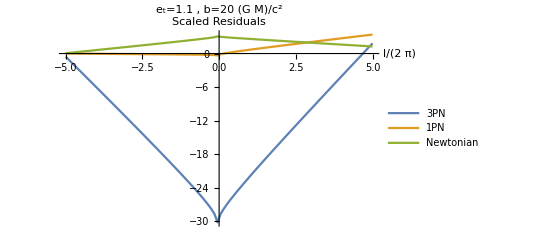

```mathematica
pres=plotres[e1,b1]
```

```mathematica
Export[StringJoin["Data3",ToString/@Riffle[{e1,b1},"_"],".dat"],Res3,ImageResolution->200];
Export[StringJoin["Data1",ToString/@Riffle[{e1,b1},"_"],".dat"],Res1,ImageResolution->200];
```

```mathematica
Export[StringJoin["DataQ",ToString/@Riffle[{e1,b1},"_"],".dat"],ResQ,ImageResolution->200];
```

```mathematica
Export[StringJoin["res",ToString/@Riffle[{e1,b1},"_"],".png"],pres,ImageResolution->200];
```